# Finite Difference Methods

## Douglas Scheme

Douglas method for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeDouglasDiagonals];

makeDouglasDiagonals[m_Integer,d_]:=
	Module[{x,y,z},
		x=Table[1.-6.*d,{m-3}];
		z=Table[1.-6.*d,{m-3}];
		y=Table[10.+12.*d,{m-2}];
{x,y,z}]
```

```mathematica
{x,y,z}=makeDouglasDiagonals[7,𝔻]
```

{{1.-6. 𝔻,1.-6. 𝔻,1.-6. 𝔻,1.-6. 𝔻},{10.+12. 𝔻,10.+12. 𝔻,10.+12. 𝔻,10.+12. 𝔻,10.+12. 𝔻},{1.-6. 𝔻,1.-6. 𝔻,1.-6. 𝔻,1.-6. 𝔻}}

```mathematica
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,5},{j,5}]//MatrixForm
```

(10.+12. 𝔻 | 1.-6. 𝔻 | 0 | 0 | 0
1.-6. 𝔻 | 10.+12. 𝔻 | 1.-6. 𝔻 | 0 | 0
0 | 1.-6. 𝔻 | 10.+12. 𝔻 | 1.-6. 𝔻 | 0
0 | 0 | 1.-6. 𝔻 | 10.+12. 𝔻 | 1.-6. 𝔻
0 | 0 | 0 | 1.-6. 𝔻 | 10.+12. 𝔻)

## Set Up Solution

#### LinearSolve Solution

```mathematica
Clear[douglasSolve];

douglasSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeDouglasDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=ListCorrelate[{1.+6.*d,10.-12.*d,1.+6.*d},#];
b[[-1]]=b[[-1]]-(1.-6.*d);
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]
]
```

## Set Parameter Values

```mathematica
Clear[𝒟,time,n,m,Δt,Δx,𝔻];
𝒟=10^-5;(*diffusion coefficient*)
time=0.1;
n=400;
𝔻=2.;(*model diffusion coefficient*)
m=Ceiling[6*√(𝔻*(n-1))];
Δt=time/n//N;
Δx=√((𝒟*Δt)/𝔻);
```

## Solve

LinearSolve solution

```mathematica
Clear[c];

Timing[
c=douglasSolve[m,n,𝔻];
c=Rest[c];]
```

{0.074268,Null}

#### Comparison with analytical result

```mathematica
p=40;(*enter a time increment*)
cb=Table[Erf[(j*Δx)/(2*Sqrt[𝒟*Δt*(p-1)])]/c⟦p,j+1⟧,{j,2,m-1}]
```

{1.00637,1.00631,1.00621,1.00609,1.00594,1.00577,1.00558,1.00538,1.00515,1.00491,1.00466,1.0044,1.00414,1.00387,1.00359,1.00332,1.00306,1.00279,1.00254,1.0023,1.00206,1.00184,1.00164,1.00144,1.00127,1.0011,1.00096,1.00082,1.0007,1.0006,1.0005,1.00042,1.00035,1.00029,1.00024,1.0002,1.00016,1.00013,1.0001,1.00008,1.00007,1.00005,1.00004,1.00003,1.00002,1.00002,1.00001,1.00001,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

## Plot current v. time

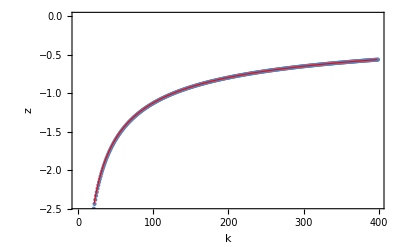

```mathematica
Clear[i,z];
i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```

## Plot concentration profiles

```mathematica
ListPlot3D[Transpose[c],PlotRange→All]
```

-Graphics3D-